# Just launch the code below to run the notebook (shift+enter)

```mathematica
ClearAll["Global`*"]
BlockEvaluation[tag_]:=Block[{},
nb=EvaluationNotebook[];
NotebookFind[nb,tag,All,CellTags];
SelectionEvaluate[nb]
]
dropdownDialog[list_,phrase_]:=DialogInput[{choice=""},Column[{TextCell[phrase],PopupMenu[Dynamic[choice],list],Button["OK",DialogReturn[choice]]}]]
infoDialog[phrase_]:=DialogInput[{choice=""},Column[{TextCell[phrase],Button["Proceed",DialogReturn[choice]]}]]
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"Auxiliary data"}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"Auxiliary data"}]]];
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"Auxiliary data/ALPs with fermion coupling"}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"Auxiliary data/ALPs with fermion coupling"}]]];
tagslist={"Evaluation","Evaluation-sensitivity"};
choiceslist={"Tabulated number of events+sensitivity","Sensitivity only"};
computationchoice=dropdownDialog[choiceslist,"Do you want to compute the tabulated number of events and then sensitivity, or just sensitivity (if the tabulate number of events has been already produced)?"];
tagselected=If[computationchoice=="Tabulated number of events+sensitivity","Evaluation","Evaluation-sensitivity"];
BlockEvaluation[tagselected]
```

# Preliminary definitions

## Parameters and various functions

```mathematica
dropdownDialog[list_,phrase_]:=DialogInput[{choice=""},Column[{TextCell[phrase],PopupMenu[Dynamic[choice],list],Button["OK",DialogReturn[choice]]}]]
infoDialog[phrase_]:=DialogInput[{choice=""},Column[{TextCell[phrase],Button["Proceed",DialogReturn[choice]]}]]
(*chbar*)
chbar= 6.6*10^-25*3*10^8;
(*Masses of various SM particles*)
mB=5.3;
mK=0.495;
mπ=0.14;
mh=125;
mBs=5.366;
(*Fragmentation fractions at the LHC*)
fbtob0LHC=fbtobplusLHC=0.324;
fbtobsLHC=0.09;
fstoK0L=1/4;
fstoKcharged=1/2;
(*Fragmentation fractions at SPS*)
fbtobsSPS=0.11;
fbtob0SPS=fbtobplusSPS=0.411;
(*Fragmentation fractions at FermilabBD. Assumed to be the same as at SPS*)
fbtobsFermilabBD=0.11;
fbtob0FermilabBD=fbtobplusFermilabBD=0.411;
```

## ALP phenomenology

## Production probability

```mathematica
(*gY = 2*Subscript[v, h]/f*)
SetDirectory[NotebookDirectory[]];
BrBplusToXsALPinclusive[ma_]=If[ma<mB-mK,Evaluate[Interpolation[Import[FileNameJoin[{NotebookDirectory[],"phenomenology/ALPs with fermion coupling/branching ratios/BplustoXsaTotal.dat"}],"Table"],InterpolationOrder->1][ma]],0];
PbbbarToALPatSPS[ma_,gY_]=(fbtobplusSPS+fbtob0SPS)*BrBplusToXsALPinclusive[ma]*gY^2;
PbbbarToALPatLHC[ma_,gY_]=(fbtobplusLHC+fbtob0LHC)*BrBplusToXsALPinclusive[ma]*gY^2;
PbbbarToALPatFermilabBD[ma_,gY_]=(fbtobplusFermilabBD+fbtob0FermilabBD)*BrBplusToXsALPinclusive[ma]*gY^2;
Print["Values of the Br ratios at m_a = 0 (α = 1 GeV, θ = 1):"]
{{"Process","B^+→X_s + a"},{"Value (g_Y = 2v_h/f = 1)", BrBplusToXsALPinclusive[0]}}//TableForm
χMotherToALPfermion[ma_,gY_,mother_,facility_]:=Association[{{ma,gY,"B","SPS"}->PbbbarToALPatSPS[ma,gY],{ma,gY,"B","FermilabBD"}->PbbbarToALPatFermilabBD[ma,gY],{ma,gY,"B","LHC"}->PbbbarToALPatLHC[ma,gY]}][{ma,gY,mother,facility}]
```

Values of the Br ratios at m_a = 0 (α = 1 GeV, θ = 1):

Process | B^+→X_s + a
Value (g_Y = 2v_h/f = 1) | 7.02209

### Maximal ALPfermion mass that may be probed by given prod. channel

```mathematica
mALPmax[mother_,facility_]:=Association[{{"B","SPS"}-> mB-mK,{"B","LHC"}-> mB-mK,{"Mixing","B","FermilabBD"}-> mB-mK}][{mother,facility}]
```

## ALPfermion lifetime and branching ratios

### Lifetimes

```mathematica
cτALPfermion[ma_,gY_]=1/gY^2 Interpolation[DeleteDuplicatesBy[Import[FileNameJoin[{NotebookDirectory[],"phenomenology/ALPs with fermion coupling/decay widths/ctauarough.txt"}],"Table"],#[[1]]&],InterpolationOrder->1][ma];
BrVisible[ECALoption_]:=If[ECALoption=="True",1,1];
ldecayALPfermion[ma_,gY_,Ea_]=(cτALPfermion[ma,gY])(√(Ea^2-ma^2)/ma);
```

### Decay br ratios

```mathematica
(*Branching ratios*)
BrRatiosALPtable=Import[FileNameJoin[{NotebookDirectory[],"phenomenology/ALPs with fermion coupling/decay widths/BrRatiosALP.txt"}],"Table"];
BrRatioALPmassless[ma_]=Interpolation[{#[[1]],#[[2]]+#[[3]]}&/@BrRatiosALPtable,InterpolationOrder->1][ma];
BrRatioALPτ[ma_]=Interpolation[{#[[1]],#[[4]]}&/@BrRatiosALPtable,InterpolationOrder->1][ma];
```

## Compilable interpolation function mapping one grid into another

### 3D to 3D

```mathematica
nd=3;
cf3=Module[{xgvars=Unique["xg"]&/@slist@@Range@nd,igvars=Unique["ig"]&/@slist@@Range@nd,tgvars=Unique["tg"]&/@slist@@Range@nd,ivars=Unique["i"]&/@slist@@Range@nd,svars=Unique["s"]&/@slist@@Range@nd,tvars=Unique["t"]&/@slist@@Range@nd,jvars=Unique["j"]&/@slist@@Range@nd},Inactivate[Compile[{seq@{xgvars,_Real,1},{y,_Real,nd}},Module[{seq@igvars,seq@tgvars,seq@ivars,seq@svars,seq@tvars},seq[igvars=Floor[xgvars]-UnitStep[xgvars-indexed@Dimensions@y]];
seq[tgvars=xgvars-igvars];
Table[seq[tvars=Compile`GetElement[tgvars,jvars]];
seq[ivars=Compile`GetElement[igvars,jvars]];
seq[svars=1.-tvars];
eval@Total[Times@@#[[All,1]] Compile`GetElement[y,Sequence@@#[[All,2]]]&/@Tuples@Transpose[{{svars,ivars},{tvars,ivars+1}},{2,3,1}]],seq@{jvars,Length@igvars}]],CompilationTarget->"C",RuntimeAttributes->{Listable},Parallelization->True,RuntimeOptions->"Speed"],Except[seq|eval|indexed]]/.seq[expr_]:>RuleCondition@(Sequence@@Table[Inactivate[expr,Except[slist|indexed]]/.{l_slist:>l[[i]],indexed[l_]:>Inactive[Compile`GetElement][l,i]},{i,nd}])/.eval@expr_:>RuleCondition[Activate[expr/.slist->List]]]//Activate;
```

### 4D to 4D

```mathematica
nd=4;
cf4=Module[{xgvars=Unique["xg"]&/@slist@@Range@nd,igvars=Unique["ig"]&/@slist@@Range@nd,tgvars=Unique["tg"]&/@slist@@Range@nd,ivars=Unique["i"]&/@slist@@Range@nd,svars=Unique["s"]&/@slist@@Range@nd,tvars=Unique["t"]&/@slist@@Range@nd,jvars=Unique["j"]&/@slist@@Range@nd},Inactivate[Compile[{seq@{xgvars,_Real,1},{y,_Real,nd}},Module[{seq@igvars,seq@tgvars,seq@ivars,seq@svars,seq@tvars},seq[igvars=Floor[xgvars]-UnitStep[xgvars-indexed@Dimensions@y]];
seq[tgvars=xgvars-igvars];
Table[seq[tvars=Compile`GetElement[tgvars,jvars]];
seq[ivars=Compile`GetElement[igvars,jvars]];
seq[svars=1.-tvars];
eval@Total[Times@@#[[All,1]] Compile`GetElement[y,Sequence@@#[[All,2]]]&/@Tuples@Transpose[{{svars,ivars},{tvars,ivars+1}},{2,3,1}]],seq@{jvars,Length@igvars}]],CompilationTarget->"C",RuntimeAttributes->{Listable},Parallelization->True,RuntimeOptions->"Speed"],Except[seq|eval|indexed]]/.seq[expr_]:>RuleCondition@(Sequence@@Table[Inactivate[expr,Except[slist|indexed]]/.{l_slist:>l[[i]],indexed[l_]:>Inactive[Compile`GetElement][l,i]},{i,nd}])/.eval@expr_:>RuleCondition[Activate[expr/.slist->List]]]//Activate;
```

# Specifying the experiment

```mathematica
SetDirectory[NotebookDirectory[]];
(*Parent directory*)
NotebookDirectory[]//ParentDirectory;
AcceptanceDirectory=FileNameJoin[{NotebookDirectory[],"Acceptances"}];
ExperimentDirectoriesList=Select[FileNames["*",AcceptanceDirectory,1],DirectoryQ];
Print["List of available experiments for which the acceptance data has been generated:"]
ExperimentsListTemp=Table[FileNameTake[ExperimentDirectoriesList[[i]],-1],{i,1,Length[ExperimentDirectoriesList],1}];
ExperimentsListTemp2=Join[Partition[ExperimentsListTemp,1],Table[{TrueQ@FileExistsQ@FileNameJoin[{NotebookDirectory[],"Acceptances",ExperimentsListTemp[[i]],ToString@StringForm["Acceptance_``_for_ALP-fermion.m",ExperimentsListTemp[[i]]]}]},{i,1,Length[ExperimentsListTemp]}],2];
ExperimentsList=Select[ExperimentsListTemp2,#[[2]]==True&][[All,1]]//Sort
If[Length[ExperimentsList]==0,Print["No experiment is available, generate first the acceptance for the given experiment using module 1"]]
Print["Selected experiment:"]
dropdownDialog[list_,phrase_]:=DialogInput[{choice=""},Column[{TextCell[phrase],PopupMenu[Dynamic[choice],list],Button["OK",DialogReturn[choice]]}]]
If[Length[ExperimentsList]≠0,SelectedExperiment=dropdownDialog[ExperimentsList,"Select the experiment:"]]
```

List of available experiments for which the acceptance data has been generated:

{FACET,MATHUSLA,SHADOWS-LoI,SHiP-ECN3}

Selected experiment:

SHiP-ECN3

## Cross-sections, acceptances

```mathematica
dataAcceptances=Import[FileNameJoin[{FileNameJoin[{NotebookDirectory[],"Acceptances",SelectedExperiment,ToString@StringForm["Acceptance_``_for_ALP-fermion.m",SelectedExperiment]}]}],"MX"];//AbsoluteTiming
FacilityGivenExperiment=dataAcceptances[[1]];
ECALoption=dataAcceptances[[2]];
BrVis[ma_]=BrVisible[ECALoption];
FullAcceptanceData0=dataAcceptances[[3]];
{θminExpAll,θmaxExpAll}=MinMax[FullAcceptanceData0[[All,2]]];
{θminExp,θmaxExp}=MinMax[Select[FullAcceptanceData0,#[[6]]≠0&][[All,2]]];
{zminExp,zmaxExp}=MinMax[FullAcceptanceData0[[All,4]]];
AzimuthalAcceptanceData=DeleteDuplicatesBy[FullAcceptanceData0,{#[[2]],#[[4]]}&][[All,{2,4,5}]];//AbsoluteTiming
θGrid=DeleteDuplicates[AzimuthalAcceptanceData[[All,1]]];
zminmaxθdata=Table[MinMax[Select[AzimuthalAcceptanceData,#[[1]]==θGrid[[i]]&&#[[3]]≠0&][[All,2]]],{i,1,Length[θGrid],1}];
zminθ[θa_]=Interpolation[Join[Partition[θGrid,1],zminmaxθdata[[All,{1}]],2],InterpolationOrder->1][θa];
zmaxθ[θa_]=Interpolation[Join[Partition[θGrid,1],zminmaxθdata[[All,{2}]],2],InterpolationOrder->1][θa];
AzimuthalAcceptanceALPfermion[θa_,za_]=Interpolation[{#[[1]],#[[2]],#[[3]]}&/@AzimuthalAcceptanceData,InterpolationOrder->1][θa,za];
DecAccDataLogarithmizedComp=Hold@Compile[{{FullAcceptanceData,_Real,2}},{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[3]]],Log10[#[[4]]],Log10[#[[6]]]}&/@FullAcceptanceData]//ReleaseHold;
DecayAcceptanceALPfermion[ma_,θa_,Ea_,za_]=BrVis[ma]*10^(Interpolation[DecAccDataLogarithmizedComp[FullAcceptanceData0],InterpolationOrder->1][Log10[ma],Log10[θa],Log10[Ea],Log10[za]]);//AbsoluteTiming
(*Interpolation for the full acceptance*)
acccomp=Hold@Compile[{{data,_Real,2}},{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[3]]],Log10[#[[4]]],If[#[[5]]*#[[6]]==0,-90,Log10[#[[5]]*#[[6]]]]}&/@SortBy[data,{#[[1]],#[[2]],#[[3]],#[[4]]}&]]//ReleaseHold;
(*Interpolation for the full acceptance*)
FullAcceptanceData=acccomp[FullAcceptanceData0];//AbsoluteTiming
FullAcceptanceALPfermion[ma_,θa_,Ea_,za_]=10^(Interpolation[FullAcceptanceData,InterpolationOrder->1][Log10[ma],Log10[θa],Log10[Ea],Log10[za]]);//AbsoluteTiming
CrossSectionsData=dataAcceptances[[4]]//Transpose;
NpotGivenExperiment=Select[CrossSectionsData,#[[1]]=="N_PoT"&][[1]][[2]];
χMother["B"]=Select[CrossSectionsData,#[[1]]=="χ_(b or OverscriptBox[b, _])"&][[1]][[2]]//N;
infoDialog[Row[{"The number of proton collisions is ", NpotGivenExperiment,". You may change it at the stage of computing the sensitivities"}]]
Row[{"Search for ALPs coupled to gluons at ", SelectedExperiment, " located at ",FacilityGivenExperiment,". N_collisions = ",NpotGivenExperiment}]
{{"Quantity","θ_min, rad","θ_max, rad","θ_min(ϵ_dec), rad","θ_max(ϵ_dec), rad","z_min, m","z_max, m"},{"Description","Min angle covered by experiment","Max angle covered by experiment","Min angle where ϵ_decay≠0","Max angle where ϵ_decay≠0","Min long. displacement of the decay volume","Max long. displacement of the decay volume"},{"Value",θminExpAll,θmaxExpAll,θminExp,θmaxExp,zminExp,zmaxExp}}//TableForm
```

{0.247262,Null}

{1.27156,Null}

{1.43307,Null}

{0.81645,Null}

{0.910936,Null}

Search for ALPs coupled to gluons at SHiP-ECN3 located at SPS. N_collisions = 6.×10^20

Quantity | θ_min, rad | θ_max, rad | θ_min(ϵ_dec), rad | θ_max(ϵ_dec), rad | z_min, m | z_max, m
Description | Min angle covered by experiment | Max angle covered by experiment | Min angle where ϵ_decay≠0 | Max angle where ϵ_decay≠0 | Min long. displacement of the decay volume | Max long. displacement of the decay volume
Value | 0.00001 | 0.0449146 | 0.00001 | 0.0449146 | 32. | 82.

# Number of events

## FIP angle-energy distributions for the given experiment

## Angle-energy distributions

```mathematica
ALPfermionDistributionFileNames:=Association[{"SPS"->{"DoubleDistr-ALPfermions-From-B-SPS.dat"},"LHC"->{"DoubleDistr-ALPfermions-From-B-LHC.dat"},"FermilabBD"->{"DoubleDistr-ALPfermions-From-B-FermilabBD.dat"}}]
ALPfermionDistributionFileNamesGivenExp=ALPfermionDistributionFileNames[FacilityGivenExperiment];
Do[If[!TrueQ@FileExistsQ@FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/ALPs with fermion coupling/",ALPfermionDistributionFileNamesGivenExp[[j]]}],Print[ALPfermionDistributionFileNamesGivenExp[[j]]," does not exist Generate it using module 2!"]
],{j,1,Length[ALPfermionDistributionFileNamesGivenExp],1}]
Clear[j]
```

### Importing distributions

```mathematica
dataDistr[filename_]:=Import[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/ALPs with fermion coupling/",filename}],"Table"]
DataDistrALPfermion["B"]=dataDistr[ALPfermionDistributionFileNamesGivenExp[[1]]];
ProductionList={"B"};
χXtoALPfermion[ma_,gY_,"B"]=χMotherToALPfermion[ma,gY,"B",FacilityGivenExperiment];
Do[
malist[prod]=DeleteDuplicates[DataDistrALPfermion[prod][[All,1]]];
{mamin[prod],mamax[prod]}=MinMax[malist[prod]];
χXtimesχXtoALPfermion[ma_,gY_,prod]=χMother[prod]*χXtoALPfermion[ma,gY,"B"];
DoubleDistrALPfermion[ma_,θa_,Ea_,prod]=10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[3]]],Log10[#[[4]]+10^-90]}&/@DataDistrALPfermion[prod],InterpolationOrder->1][Log10[ma],Log10[θa],Log10[Ea]]),{prod,ProductionList}
]
```

### Determining min/max energies of ALPfermions for the given polar angle. Needed for stability of Monte-Carlo integration

#### Common definition

InterpolatingFunction::dmval: Input value {0.05} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{4.90288,Null}

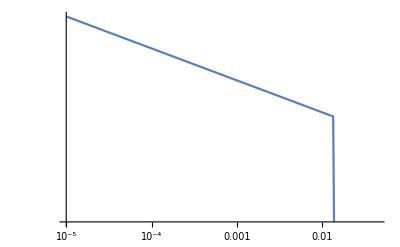

```mathematica
EfromXmax[mass_,data_,LogMin_]:=Module[{distr},
datt=Select[data,#[[1]]==mass&];
EmaxVal=datt[[All,3]]//Max;
θlist=Table[x,{x,θminExp,θmaxExp,(θmaxExp-θminExp)/5}];
distr[θfip_,Efip_]=Abs[Evaluate[Interpolation[{#[[2]],#[[3]],#[[4]]+10^-90}&/@datt,InterpolationOrder->1][θfip,Efip]]];
DoubleDistrIntList[i_]:=Interpolation[ParallelTable[{Efip,Quiet[NIntegrate[distr[θfip,Efip],{θfip,θlist[[i]],θlist[[i+1]]},Method->"AdaptiveMonteCarlo"]]},{Efip,Table[10^x,{x,Log10[1.1*mass],Log10[EmaxVal],(Log10[EmaxVal]-Log10[1.1*mass])/50.}]}],InterpolationOrder->1][Efip];
θfipdistrlist[Efip_]=Table[{(θlist[[i]]+θlist[[i+1]])/2,DoubleDistrIntList[i]},{i,1,Length[θlist]-1,1}];
θEmaxList=Table[{θfipdistrlist[Efip][[i]][[1]],SortBy[Table[{Efip,θfipdistrlist[Efip][[i]][[2]]},{Efip,mass,EmaxVal,1}],-#[[2]]&][[1]][[1]]},{i,1,Length[θfipdistrlist[Efip]],1}];
θEmaxListInt[θfip_]=Interpolation[θEmaxList,InterpolationOrder->1][θfip];
NormVals=Table[NIntegrate[θfipdistrlist[Efip][[i]][[2]]+10^-90.,{Efip,mass,EmaxVal},Method->"InterpolationPointsSubdivision"],{i,1,Length[θfipdistrlist[Efip]],1}];
cdf[es_,i_]:=1-1/NormVals[[i]] NIntegrate[θfipdistrlist[Efip][[i]][[2]],{Efip,mass,es},Method->"InterpolationPointsSubdivision"];
cdftab[Efip_]=Table[{θfipdistrlist[Efip][[i]][[1]],Interpolation[ParallelTable[{10^es,Quiet[cdf[10^es,i]]},{es,Log10[mass],Log10[EmaxVal],(Log10[EmaxVal]-Log10[mass])/50}],InterpolationOrder->1][Efip]},{i,1,Length[θfipdistrlist[Efip]],1}];
logmin[θfip_]=LogMin;
Estart[θfip_]=Min[2*θEmaxListInt[θfip],0.9*EmaxVal];
Emaxv[i_]:=If[NormVals[[i]]<10^-15,mass,10^(Efip/.FindRoot[Log10[cdftab[10^Efip][[i]][[2]]]==logmin[θEmaxList[[i]][[1]]],{Efip,Log10[Estart[θEmaxList[[i]][[1]]]],Log10[θEmaxList[[i]][[2]]],Log10[EmaxVal]}])];
tabtemp=Table[{θEmaxList[[i]][[1]],Emaxv[i]},{i,1,Length[θEmaxList],1}];
tab=Join[{{θminExp,tabtemp[[1]][[2]]}},Drop[Drop[tabtemp,1],-1],{{θmaxExp,tabtemp[[-1]][[2]]}}];
10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]]}&/@tab,InterpolationOrder->1][Log10[θfip]])
]
EmaxBlock[data_,logmin_]:=Module[{mlist},
mlist=Drop[data[[All,1]],-1];
EmaxTemp[m_,θ_]=Max[m,EfromXmax[mlist[[1]],data,logmin],EfromXmax[mlist[[-1]],data,logmin]]/.{θfip->θ};
θlist=Table[x,{x,θminExp,θmaxExp,(θmaxExp-θminExp)/10}];
10^(Interpolation[{#[[1]],Log10[#[[2]]],Log10[#[[3]]]}&/@Flatten[Table[{mfip,θfip,EmaxTemp[mfip,θfip]},{mfip,mlist[[1]],mlist[[-1]],(mlist[[-1]]-mlist[[1]])/10},{θfip,θlist}],{1,2}],InterpolationOrder->1][mfip,Log10[θfip]])
]
Do[Eamax[mfip_,θfip_,prod]=EmaxBlock[DataDistrALPfermion[prod],-7],{prod,ProductionList}]//AbsoluteTiming
LogLogPlot[Evaluate[Table[Eamax[0.1,θa,prod],{prod,ProductionList}]],{θa,θminExp,θmaxExp}]
```

## Number of events

## Definitions

### Grids for the initial data with acceptances and distributions

```mathematica
(*Grid Subscript[m, S], Subscript[θ, S], Subscript[E, S], Subscript[z, S] for the initial acceptance data, logarithmized*)
InGridmϵ=DeleteDuplicates[FullAcceptanceData[[All,1]]];
InGridθϵ=DeleteDuplicates[FullAcceptanceData[[All,2]]];
InGridEϵ=DeleteDuplicates[FullAcceptanceData[[All,3]]];
InGridzϵ=DeleteDuplicates[FullAcceptanceData[[All,4]]];
(*Array of values of the initial acceptance data, reshaped*)
ϵvals=ArrayReshape[FullAcceptanceData[[All,5]],{Length[InGridmϵ],Length[InGridθϵ],Length[InGridEϵ],Length[InGridzϵ]}];
ϵazValscomp=Compile[{{data,_Real,2}},Table[If[data[[i]][[5]]==0,-90.,Log10[data[[i]][[5]]]],{i,1,Length[data],1}],CompilationTarget->"C",RuntimeOptions->"Speed"];
ϵazvals=ArrayReshape[ϵazValscomp[FullAcceptanceData0],{Length[InGridmϵ],Length[InGridθϵ],Length[InGridEϵ],Length[InGridzϵ]}];
(*_________________________________________________________________*)
(*Grid Subscript[m, S], Subscript[θ, S], Subscript[E, S] for the initial FIP distribution data, logarithmized*)
DataLogarithmiedComp=Hold@Compile[{{data,_Real,2}},Table[If[data[[i]][[4]]==0,-90.,Log10[data[[i]][[4]]]],{i,1,Length[data],1}],CompilationTarget->"C",RuntimeOptions->"Speed"]//ReleaseHold
BlockGridsValsDistr[ProdChannel_]:=Module[{GridIn,vals},
GridIn=Log10[DeleteDuplicates[DataDistrALPfermion[ProdChannel][[All,#]]]&/@{1,2,3}];
vals=ArrayReshape[DataLogarithmiedComp[DataDistrALPfermion[ProdChannel]],{Length[GridIn[[1]]],Length[GridIn[[2]]],Length[GridIn[[3]]]}];
{GridIn,vals}
]
Do[{GridInFinal[prod],DistrVals[prod]}=BlockGridsValsDistr[prod],{prod,ProductionList}];//AbsoluteTiming
```

CompiledFunction[…]

{0.015041,Null}

### Grid to be used to calculate the number of events

```mathematica
(*Grid Subscript[θ, S], Subscript[z, S] for the final acceptance data, logarithmized*)
OutGridθfinal=(*InGridθϵ*)Log10[Table[x,{x,10^Min[InGridθϵ],10^Max[InGridθϵ],(10^Max[InGridθϵ]-10^Min[InGridθϵ])/30}]];
OutGridzfinal=Log10[Table[x,{x,10^InGridzϵ[[1]],10^InGridzϵ[[-1]],Min[(10^InGridzϵ[[-1]]-10^InGridzϵ[[1]])/5,Max[0.5,(10^InGridzϵ[[-1]]-10^InGridzϵ[[1]])/30]]}]](*InGridzϵ*);
ΔxVals[list_]:=Join[{(list[[2]]-list[[1]])/2},Table[list[[i]]-list[[i-1]],{i,2,Length[list],1}]];
Δθvals=ΔxVals[10^OutGridθfinal];
Δzvals=ΔxVals[10^OutGridzfinal];
(*Final energy grid. Mass- and production channel-dependent*)
StepEtemp[Efip_]=Piecewise[{{0.3,Efip≤2.5},{0.5,2.5<Efip<35},{2,35≤Efip≤50},{4,50<Efip<160},{5,160≤Efip<300},{40,300≤Efip<700},{50,700≤Efip<2000},{200,2000≤Efip<4000},{400,4000≤Efip<7000},{500,7000≤Efip≤50000}}];
OutGridEnergy[m_,ProdChannel_]:=Block[{},
With[{start=1.01m,end=Eamax[m,θminExp,ProdChannel]},
Log10[NestWhileList[#+StepEtemp[#]&,start,#≤end&,1,∞,-1]]]//N
]
ΔxValsTotComp=Hold@Compile[{{Δθvals,_Real,1},{ΔEvals,_Real,1},{Δzvals,_Real,1}},Table[{Δθvals[[i]]*ΔEvals[[j]]*Δzvals[[k]]},{i,1,Length[Δθvals]},{j,1,Length[ΔEvals]},{k,1,Length[Δzvals]}],CompilationTarget->"C",RuntimeOptions->"Speed"]//ReleaseHold;
```

### Code that computes the number of events - using the mapping method

#### Grid for distribution times acceptance

```mathematica
(*Block that computes the grid Subscript[θ, S],Subscript[E, S],Subscript[z, S], Subscript[ϵ, Full]×Subscript[f, Subscript[θ, S],Subscript[E, S]]*)
TableIntegrandDiscret[m_,ProdChannel_,ϵDecOp_]:=Block[{},
OutGridEfinal=OutGridEnergy[N[m],ProdChannel];
ΔEvals=ΔxVals[10^OutGridEfinal];
ΔxValsTot=Flatten[ΔxValsTotComp[Δθvals,ΔEvals,Δzvals],{1,2,3}];
OutGridFinal=Tuples[{{Log10[N[m]]},OutGridθfinal,OutGridEfinal,OutGridzfinal}];
OutGridFinal1=10^OutGridFinal[[All,{2,3,4}]];
gϵ={InGridmϵ,InGridθϵ,InGridEϵ,InGridzϵ};
xgϵ={{Log10[N[m]]},OutGridθfinal,OutGridEfinal,OutGridzfinal};
xigϵ=MapThread[Interpolation[Transpose@{#,Range@Length@#},InterpolationOrder->1][#2]&,{gϵ,xgϵ}];
ϵResult=10^Flatten@cf4[Sequence@@xigϵ,If[ϵDecOp=="True",ϵvals,ϵazvals]];
gDistr={GridInFinal[ProdChannel][[1]],GridInFinal[ProdChannel][[2]],GridInFinal[ProdChannel][[3]]};
xgDistr={{Log10[N[m]]},OutGridθfinal,OutGridEfinal};
xigDistr=MapThread[Interpolation[Transpose@{#,Range@Length@#},InterpolationOrder->1][#2]&,{gDistr,xgDistr}];
DistrResult=10^Flatten@cf3[Sequence@@xigDistr,DistrVals[ProdChannel]];
TabTemp0=Join[OutGridFinal1,List/@Flatten[DistrResult Partition[ϵResult,Length[OutGridzfinal]]],ΔxValsTot,2]
]
```

#### Convoluting acceptances with pre-factor

```mathematica
(*Values Subscript[f, FIP]×Subscript[ϵ, FIP]×Exp[-Subscript[z, FIP]/(cos(Subscript[θ, FIP])Subscript[cτ, FIP] Subscript[p, FIP]/Subscript[m, FIP])]/(cos(Subscript[θ, FIP])Subscript[cτ, FIP] Subscript[p, FIP]/Subscript[m, FIP])×Subscript[ϵ, decay] Subscript[Δz, FIP] Subscript[ΔE, FIP] Subscript[Δθ, FIP] for the grid of values Subscript[θ, FIP], Subscript[E, FIP], Subscript[z, FIP] fixed values of Subscript[cτ, FIP] and Subscript[m, FIP]*)
tableprefac=Hold@Compile[{{tabb,_Real,1},{m,_Real},{cτ,_Real},{decProb,_Integer}},Module[{angles,energies,zv,values,Δs,prefactor},
values=Compile`GetElement[tabb,4];
Δs=Compile`GetElement[tabb,5];
If[decProb==1,
angles=Compile`GetElement[tabb,1];
energies=Compile`GetElement[tabb,2];
zv=Compile`GetElement[tabb,3];
prefactor=Exp[-zv/(Cos[angles]*cτ*(√(energies^2-m^2))/m)]/(Cos[angles]*cτ*(√(energies^2-m^2))/m),prefactor=1.];
prefactor*Δs*values],CompilationTarget->"C",RuntimeOptions->"Speed",Parallelization->"True",RuntimeAttributes->{Listable}]//ReleaseHold;
(*Summation of the values above*)
sumcompile=Hold@Compile[{{tabcτm,_Real,1}},Total[tabcτm],CompilationTarget->"C",RuntimeOptions->"Speed",Parallelization->"True"]//ReleaseHold;
{mminϵ,mmaxϵ}=10^MinMax[InGridmϵ]
```

{0.02,4.7}

#### Acceptances

```mathematica
FactorANUBISceiling=If[SelectedExperiment=="ANUBIS-ceiling",2,1];
AcceptanceDiscret[m_,ProdChannel_,ϵdecOp_,decProb_]:=Module[{NevDiscret,NpotTimesχval},
If[Max[mamin[ProdChannel],mminϵ]<m<Min[mamax[ProdChannel],mmaxϵ],
integrandtab=TableIntegrandDiscret[m,ProdChannel,ϵdecOp];
brvis=If[ϵdecOp==1,BrVis[m],1];
(*Test lifetime for the acceptance*)
cτacc=10^9;
(*Prefactor for the acceptance. If only azimuthal and *)
prefacacc=If[decProb==1,cτacc,1/(zmaxExp-zminExp)];
accdiscret=If[brvis!=0,FactorANUBISceiling*brvis*prefacacc*sumcompile[tableprefac[integrandtab,m,cτacc,decProb]],0],accdiscret=0];
accdiscret
]
```

## Acceptances and approximate lower/upper bounds computation

{3.05378,Null}

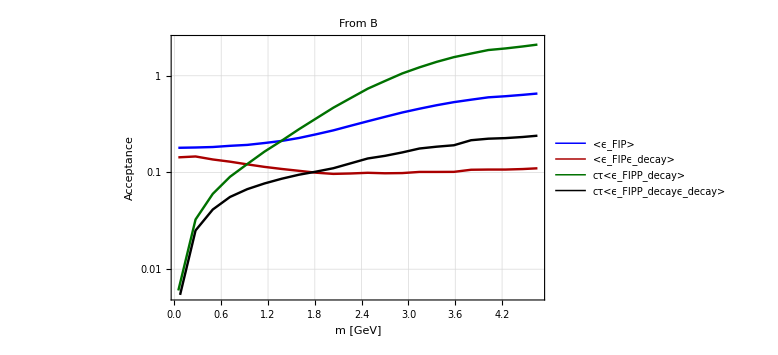

```mathematica
Do[mlistAcceptance[prod]=Join[Table[m,{m,1.01Max[mamin[prod],mminϵ],0.95Min[mamax[prod],mmaxϵ],Min[(0.95Min[mamax[prod],mmaxϵ]-1.01Max[mamin[prod],mminϵ])/20,2]}],{0.99Min[mamax[prod],mmaxϵ]}],{prod,ProductionList}];
Do[ϵGeomTabs[prod]=Table[{m,AcceptanceDiscret[m,prod,"False",0],AcceptanceDiscret[m,prod,"True",0],AcceptanceDiscret[m,prod,"False",1],AcceptanceDiscret[m,prod,"True",1]},{m,mlistAcceptance[prod]}],{prod,ProductionList}];//AbsoluteTiming
PlotAcc[ProdChannel_]:=ListLogPlot[{ϵGeomTabs[ProdChannel][[All,{1,2}]],ϵGeomTabs[ProdChannel][[All,{1,3}]],ϵGeomTabs[ProdChannel][[All,{1,4}]],ϵGeomTabs[ProdChannel][[All,{1,5}]]},FrameStyle->Directive[Black, 22],PlotStyle->{{Thickness[0.003],Blue},{Thickness[0.003],Darker@Red},{Thickness[0.003],Darker@Darker@Green},{Thickness[0.003],Black}},GridLines->Automatic,PlotRange->{MinMax[ϵGeomTabs[ProdChannel][[All,1]]],{0.9Min[Min[ϵGeomTabs[ProdChannel][[All,4]]],Min[ϵGeomTabs[ProdChannel][[All,3]]]],1.1Max[Max[ϵGeomTabs[ProdChannel][[All,2]]],Max[ϵGeomTabs[ProdChannel][[All,4]]]]}},Joined->True,Frame->True,ImageSize->Large,FrameLabel->{"m [GeV]","Acceptance"},PlotLabel-> Style[Row[{"From ",ProdChannel}], 20, Black],PlotLegends->Placed[{Style[#, 18]&/@{"<ϵ_FIP>","<ϵ_FIPϵ_decay>","cτ<ϵ_FIPP_decay>","cτ<ϵ_FIPP_decayϵ_decay>"}},{0.75,0.2}]]
Style[Row[Evaluate[Table[PlotAcc[prod],{prod,ProductionList}]]],ImageSizeMultipliers->{1,1,1,1}]
Do[FilenameAcceptance[prod]=ToString@StringForm["Acceptance_ALP-fermion_at_``_From_``.dat",Sequence@@{SelectedExperiment,prod}];
Export[FileNameJoin[{NotebookDirectory[],"Auxiliary data/ALPs with fermion coupling",SelectedExperiment,FilenameAcceptance[prod]}],ϵGeomTabs[prod][[All,{1,2,4,5}]],"Table"]
,{prod,ProductionList}]
```

### Rough estimates of the upper and lower bounds

#### Definitions

InterpolatingFunction::dmval: Input value {0.0500046} lies outside the range of data in the interpolating function. Extrapolation will be used.

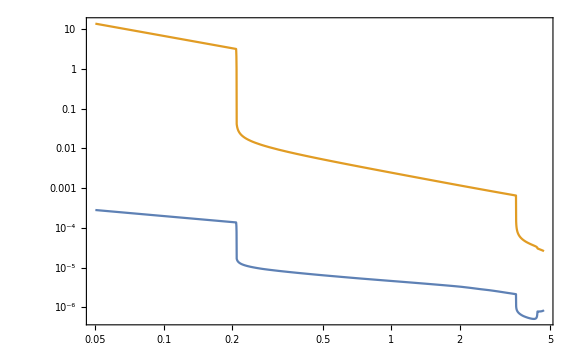

```mathematica
Do[gYminEstimate[ma_,prod]=((NpotGivenExperiment*χXtimesχXtoALPfermion[ma,1,prod]*Interpolation[ϵGeomTabs[prod][[All,{1,5}]],InterpolationOrder->1][ma])/(2.3ldecayALPfermion[ma,1,Ea]*ma/(√(Ea^2-ma^2))))^(-1/4.);
gYmaxEstimate[ma_,prod]=√Re[Evaluate[-ProductLog[-1,-2.3*b/a]/b/.{a-> NpotGivenExperiment*χXtimesχXtoALPfermion[ma,1,prod]*Interpolation[ϵGeomTabs[prod][[All,{1,3}]],InterpolationOrder->1][ma],b->zminExp/ldecayALPfermion[ma,1,Eamax[malist[prod][[1]],θminExp,prod]]}]],{prod,ProductionList}]
ϵestplot="B";
LogLogPlot[{gYminEstimate[ma,ϵestplot],gYmaxEstimate[ma,ϵestplot]},{ma,Min[malist[ϵestplot]],Max[malist[ϵestplot]]},Frame->True,ImageSize->Large]
```

## Number of events

### Fast

```mathematica
FactorLowerBound=If[MemberQ[{"ANUBIS-shaft-volume-1","ANUBIS-shaft-volume-2","ANUBIS-shaft-volume-3"},SelectedExperiment]==True,0.1,0.3];
NeventsDiscret[m_,ProdChannel_,gYlist_]:=Module[{NevDiscret,NpotTimesχval},
If[Max[mminϵ,mamin[ProdChannel]]<m<Min[mamax[ProdChannel],mmaxϵ],
integrandtab=TableIntegrandDiscret[m,ProdChannel,"True"];
NpotTimesχval[gY_]=FactorANUBISceiling*NpotGivenExperiment*χXtimesχXtoALPfermion[m,gY,ProdChannel];
{lowerbound,upperbound}={gYminEstimate[m,ProdChannel],gYmaxEstimate[m,ProdChannel]};
brvis=BrVis[m];
NevDiscret[gY_]:=If[brvis!=0,If[FactorLowerBound*lowerbound<gY<1.5upperbound,NpotTimesχval[gY]*brvis*sumcompile[tableprefac[integrandtab,m,cτALPfermion[m,gY],1]],0],0];
Table[{m,gYlist[[i]],NevDiscret[gYlist[[i]]]},{i,1,Length[gYlist],1}],Table[{m,gYlist[[i]],0},{i,1,Length[gYlist],1}]]
]
```

### Slow, using built-in Mathematica functions Interpolation, NIntegrate

```mathematica
(*Differential decay probability 1/ldecay Exp[-l/ldecay], where l is expressed in terms of the longitudinal displacement z and polar angle θ as z/cosθ*)
PdecayDensity[ma_,gY_,θa_,Ea_,za_]=Exp[-za/(Cos[θa]*ldecayALPfermion[ma,gY,Ea])]/(Cos[θa]*ldecayALPfermion[ma,gY,Ea]);
(*The integrand determining the differential rate for events*)
Do[IntegrandALPfermion[ma_,gY_,θa_,Ea_,za_,prod]=DoubleDistrALPfermion[ma,θa,Ea,prod]*PdecayDensity[ma,gY,θa,Ea,za]*AzimuthalAcceptanceALPfermion[θa,za]*Min[DecayAcceptanceALPfermion[ma,θa,Ea,za],1],{prod,ProductionList}];
IntegralALPfermion[ma_,gY_,ProdChannel_]:=NIntegrate[Abs[IntegrandALPfermion[ma,gY,θa,Ea,z,ProdChannel]],{θa,θminExp,θmaxExp},{Ea,ma,Eamax[ma,θa,ProdChannel]},{z,zminθ[θa],zmaxθ[θa]},Method->"AdaptiveMonteCarlo"]
gYvall=10^-15;
Nevents[ma_,gY_,ProdChannel_]:=If[mamin[ProdChannel]≤ma≤mamax[ProdChannel],If[FactorLowerBound*gYminEstimate[ma,ProdChannel]<gY<1.8gYmaxEstimate[ma,ProdChannel],NpotGivenExperiment*χXtimesχXtoALPfermion[ma,gY,ProdChannel]*IntegralALPfermion[ma,gY,ProdChannel],0],0]
```

#### Test

```mathematica
(*This is a comparison between the slow and fast integration methods. For the selected mass and production channel, the numbers of events obtained using the methods should agree within 10%*)
(*If the agreement is worse, there may be a few reasons*)
(*1) The grid for the fast method is not dense enough. Try to increase the grid density (OutGridθfinal, OutGridEfinal, OutGridzfinal) to see whether the agreement improves. Sometimes, even a slightly denser grid for e.g. z may lead to a significant improvement in the agrement*)
(*2) The Monte-Carlo integrator for the slow method fails to evaluate properly; this may happen if the range of the integration over energies is too large compared to the domain where most of the events actually are (off-axis experiments such as MATHUSLA and ANUBIS). Another symptom is that for the given mass and coupling the integral "jumps", i.e., returns values with large error*)
mtest=0.4;
ProdTest="B";
gYlist=(*{10^-12,3*10^-12,5*10^-12,10^-11,5*10^-11,10^-10,5*10^-10,10^-9,5*10^-9,10^-8,2*10^-8,4*10^-8,10^-7,5*10^-7,6*10^-7,7*10^-7,8*10^-7,9*10^-7,10^-6,2*10^-6}//N*)Table[10^x,{x,-17.,-1.,0.2}];
dat1=NeventsDiscret[mtest,ProdTest,gYlist];//AbsoluteTiming
dat2=ParallelTable[{gYlist[[i]],cτALPfermion[mtest,gYlist[[i]]],Nevents[mtest,gYlist[[i]],ProdTest]},{i,1,Length[gYlist],1}];//AbsoluteTiming
Join[dat1,dat2[[All,{3,2}]],2]//TableForm
```

{0.253382,Null}

{6.17057,Null}

0.4 | 1.×10^-17 | 0 | 0 | 7.75616×10^26
0.4 | 1.58489×10^-17 | 0 | 0 | 3.08778×10^26
0.4 | 2.51189×10^-17 | 0 | 0 | 1.22927×10^26
0.4 | 3.98107×10^-17 | 0 | 0 | 4.89381×10^25
0.4 | 6.30957×10^-17 | 0 | 0 | 1.94826×10^25
0.4 | 1.×10^-16 | 0 | 0 | 7.75616×10^24
0.4 | 1.58489×10^-16 | 0 | 0 | 3.08778×10^24
0.4 | 2.51189×10^-16 | 0 | 0 | 1.22927×10^24
0.4 | 3.98107×10^-16 | 0 | 0 | 4.89381×10^23
0.4 | 6.30957×10^-16 | 0 | 0 | 1.94826×10^23
0.4 | 1.×10^-15 | 0 | 0 | 7.75616×10^22
0.4 | 1.58489×10^-15 | 0 | 0 | 3.08778×10^22
0.4 | 2.51189×10^-15 | 0 | 0 | 1.22927×10^22
0.4 | 3.98107×10^-15 | 0 | 0 | 4.89381×10^21
0.4 | 6.30957×10^-15 | 0 | 0 | 1.94826×10^21
0.4 | 1.×10^-14 | 0 | 0 | 7.75616×10^20
0.4 | 1.58489×10^-14 | 0 | 0 | 3.08778×10^20
0.4 | 2.51189×10^-14 | 0 | 0 | 1.22927×10^20
0.4 | 3.98107×10^-14 | 0 | 0 | 4.89381×10^19
0.4 | 6.30957×10^-14 | 0 | 0 | 1.94826×10^19
0.4 | 1.×10^-13 | 0 | 0 | 7.75616×10^18
0.4 | 1.58489×10^-13 | 0 | 0 | 3.08778×10^18
0.4 | 2.51189×10^-13 | 0 | 0 | 1.22927×10^18
0.4 | 3.98107×10^-13 | 0 | 0 | 4.89381×10^17
0.4 | 6.30957×10^-13 | 0 | 0 | 1.94826×10^17
0.4 | 1.×10^-12 | 0 | 0 | 7.75616×10^16
0.4 | 1.58489×10^-12 | 0 | 0 | 3.08778×10^16
0.4 | 2.51189×10^-12 | 0 | 0 | 1.22927×10^16
0.4 | 3.98107×10^-12 | 0 | 0 | 4.89381×10^15
0.4 | 6.30957×10^-12 | 0 | 0 | 1.94826×10^15
0.4 | 1.×10^-11 | 0 | 0 | 7.75616×10^14
0.4 | 1.58489×10^-11 | 0 | 0 | 3.08778×10^14
0.4 | 2.51189×10^-11 | 0 | 0 | 1.22927×10^14
0.4 | 3.98107×10^-11 | 0 | 0 | 4.89381×10^13
0.4 | 6.30957×10^-11 | 0 | 0 | 1.94826×10^13
0.4 | 1.×10^-10 | 0 | 0 | 7.75616×10^12
0.4 | 1.58489×10^-10 | 0 | 0 | 3.08778×10^12
0.4 | 2.51189×10^-10 | 0 | 0 | 1.22927×10^12
0.4 | 3.98107×10^-10 | 0 | 0 | 4.89381×10^11
0.4 | 6.30957×10^-10 | 0 | 0 | 1.94826×10^11
0.4 | 1.×10^-9 | 0 | 0 | 7.75616×10^10
0.4 | 1.58489×10^-9 | 0 | 0 | 3.08778×10^10
0.4 | 2.51189×10^-9 | 0 | 0 | 1.22927×10^10
0.4 | 3.98107×10^-9 | 0 | 0 | 4.89381×10^9
0.4 | 6.30957×10^-9 | 0 | 0 | 1.94826×10^9
0.4 | 1.×10^-8 | 0 | 0 | 7.75616×10^8
0.4 | 1.58489×10^-8 | 0 | 0 | 3.08778×10^8
0.4 | 2.51189×10^-8 | 0 | 0 | 1.22927×10^8
0.4 | 3.98107×10^-8 | 0 | 0 | 4.89381×10^7
0.4 | 6.30957×10^-8 | 0 | 0 | 1.94826×10^7
0.4 | 1.×10^-7 | 0 | 0 | 7.75616×10^6
0.4 | 1.58489×10^-7 | 0 | 0 | 3.08778×10^6
0.4 | 2.51189×10^-7 | 0 | 0 | 1.22927×10^6
0.4 | 3.98107×10^-7 | 0 | 0 | 489381.
0.4 | 6.30957×10^-7 | 0 | 0 | 194826.
0.4 | 1.×10^-6 | 0 | 0 | 77561.6
0.4 | 1.58489×10^-6 | 0 | 0 | 30877.8
0.4 | 2.51189×10^-6 | 0.033914 | 0.0347678 | 12292.7
0.4 | 3.98107×10^-6 | 0.213974 | 0.215731 | 4893.81
0.4 | 6.30957×10^-6 | 1.34994 | 1.38645 | 1948.26
0.4 | 0.00001 | 8.51529 | 8.49201 | 775.616
0.4 | 0.0000158489 | 53.6921 | 53.9518 | 308.778
0.4 | 0.0000251189 | 338.208 | 341.528 | 122.927
0.4 | 0.0000398107 | 2125.01 | 2099.4 | 48.9381
0.4 | 0.0000630957 | 13267.5 | 13392.3 | 19.4826
0.4 | 0.0001 | 81538. | 79882. | 7.75616
0.4 | 0.000158489 | 481918. | 479150. | 3.08778
0.4 | 0.000251189 | 2.59178×10^6 | 2.63093×10^6 | 1.22927
0.4 | 0.000398107 | 1.12208×10^7 | 1.12117×10^7 | 0.489381
0.4 | 0.000630957 | 3.08919×10^7 | 3.03843×10^7 | 0.194826
0.4 | 0.001 | 3.73175×10^7 | 3.70896×10^7 | 0.0775616
0.4 | 0.00158489 | 1.19278×10^7 | 1.18675×10^7 | 0.0308778
0.4 | 0.00251189 | 467353. | 472989. | 0.0122927
0.4 | 0.00398107 | 508.491 | 506.023 | 0.00489381
0.4 | 0.00630957 | 0.000350004 | 0.000409369 | 0.00194826
0.4 | 0.01 | 2.0073×10^-18 | 5.08075×10^-18 | 0.000775616
0.4 | 0.0158489 | 0 | 0 | 0.000308778
0.4 | 0.0251189 | 0 | 0 | 0.000122927
0.4 | 0.0398107 | 0 | 0 | 0.0000489381
0.4 | 0.0630957 | 0 | 0 | 0.0000194826
0.4 | 0.1 | 0 | 0 | 7.75616×10^-6

### Differential number of events

CompiledFunction[…]

{0.505,343.105}

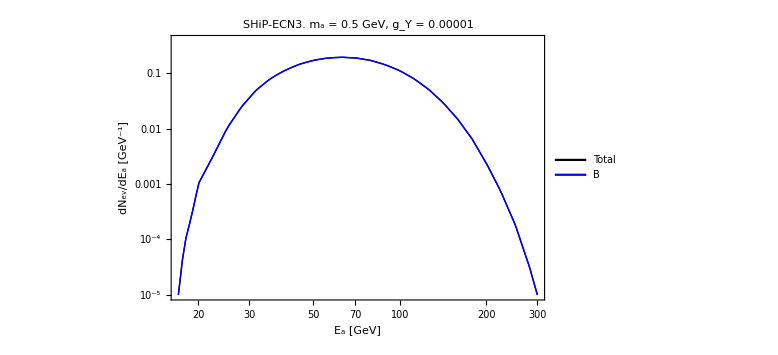

```mathematica
(*The same as tableprefac but also including the grid*)
tableGridPrefac=Hold@Compile[{{tabb,_Real,2},{mS,_Real},{cτ,_Real}},{#[[1]],#[[2]],#[[3]],Exp[-#[[3]]/(Cos[#[[1]]]*cτ*(√((#[[2]])^2-mS^2))/mS)]/(Cos[#[[1]]]*cτ*(√((#[[2]])^2-mS^2))/mS)#[[4]]*#[[5]]}&/@tabb,CompilationTarget->"C",RuntimeOptions->"Speed",Parallelization->"True",RuntimeAttributes->{Listable}]//ReleaseHold;
(*Summation returning the differential number of events X, df/dX *)
NdiffCompiled=Hold@Compile[{{tabNdiff,_Real,2},{GridQuantity,_Real,1},{LengthPerVariable,_Integer},{NPoTtimesPprod,_Real}},Table[{tabNdiff[[LengthPerVariable*(i-1)+1]][[1]],NPoTtimesPprod*Sum[tabNdiff[[LengthPerVariable*(i-1)+j]][[4]],{j,1,LengthPerVariable,1}]},{i,1,Length[GridQuantity],1}],CompilationTarget->"C",RuntimeOptions->"Speed",Parallelization->"True"]//ReleaseHold
(*Variable = "E_X","x_x","θ_X". The number belongs to the column in the tabulated data*)
iVal:=Association[{"E_X" ->2,"θ_X"->1,"x_x"->3}]
(*Differential number of events*)
NeventsDifferentialDiscret[m_,ProdChannel_,gY_,Variable_]:=Module[{NpotTimesχval},
ival=iVal[Variable];
NpotTimesχval=NpotGivenExperiment*χXtimesχXtoALPfermion[m,gY,ProdChannel];
tablegrid0=TableIntegrandDiscret[m,ProdChannel,"True"];
Δxvals:=Association[{"E_X"->ΔEvals,"θ_X"-> Δθvals,"x_X"-> Δzvals}];
Δxval=Δxvals[Variable];
cτVal=cτALPfermion[m,gY];
brvis=BrVis[m];
ilist=DeleteDuplicates[{ival,1,2,3}];
tablegrid1=SortBy[{#[[ilist[[1]]]],#[[ilist[[2]]]],#[[ilist[[3]]]],#[[4]]}&/@tableGridPrefac[tablegrid0,m,cτVal],{#[[1]],#[[2]],#[[3]]}&];
GridQuantity=tablegrid1[[All,1]]//DeleteDuplicates;
LengthPerVariable=Length[tablegrid1]/Length[GridQuantity];
tab1=NdiffCompiled[tablegrid1,GridQuantity,LengthPerVariable,NpotTimesχval*brvis];
Join[tab1[[All,{1}]],Partition[tab1[[All,2]]*Δxval^-1,1],2]
]
mvaltest=0.5;
gYtest=10^-5;
quantity="E_X";
LegendX:=Association[{"E_X"->"E_a [GeV]","θ_X"->"θ_a [rad]","x_X"-> "z_a [m]"}]
LegendY:=Association[{"E_X"->"dN_ev/dE_a [GeV^-1]","θ_X"->"dN_ev/dθ_a [rad^-1]","x_X"-> "dN_ev/dz_a [m^-1]"}]
prodlisttemp={};
Do[If[Max[mamin[prod],mminϵ]<mvaltest<Min[mamax[prod],mmaxϵ],
prodlisttemp=Join[prodlisttemp,{prod}];
NdiffData[prod]=NeventsDifferentialDiscret[mvaltest,prod,gYtest,quantity];
XvalminmaxNdiff=Select[NdiffData[prod],#[[2]]>10^-40&][[All,1]]//MinMax;
NdiffInt[X_,prod]=If[XvalminmaxNdiff[[1]]<X<XvalminmaxNdiff[[2]],Evaluate[10^Interpolation[{Log10[#[[1]]],Log10[#[[2]]+10^-90]}&/@NdiffData[prod],InterpolationOrder->1][Log10[X]]],0]],{prod,ProductionList}];
NdiffInt[X_,"Total"]=Sum[NdiffInt[X,prod],{prod,prodlisttemp}];
LegendList=Join[{"Total"},prodlisttemp];
QuantityMinMax=Flatten[Table[MinMax[NdiffData[prod][[All,1]]],{prod,prodlisttemp}],1]//MinMax
ValueMinMax=Max[Max[NdiffData[#][[All,2]]]&/@prodlisttemp];
LogLogPlot[Evaluate[Table[NdiffInt[X,prod],{prod,LegendList}]],{X,QuantityMinMax[[1]],QuantityMinMax[[2]]},Frame->True,ImageSize->Large,PlotRange->{All,{10^-5,2ValueMinMax}},PlotStyle->{{Thick,Black},{Thick,Blue},{Thick,Darker@Red},{Thick,Darker@Darker@Green},{Thick,Darker@Cyan},{Thick,Magenta},{Thick,Blue,Dashing[0.02]},{Thick,Darker@Red,Dashing[0.02]},{Thick,Darker@Darker@Green,Dashing[0.02]}},PlotLegends->Placed[Style[#,20]&/@LegendList,{0.85,0.7}],FrameLabel->{LegendX[quantity] ,LegendY[quantity]},FrameStyle->Directive[Black, 23],PlotLabel->Style[Row[{SelectedExperiment,". m_a = ",mvaltest," GeV, g_Y = ",(gYtest//N)}],20,Black]]
```

# Exporting tabulated number of events

## Definitions

```mathematica
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"Tabulated Nevents"}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"Tabulated Nevents"}]]];
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"Tabulated Nevents/ALPs with fermion coupling"}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"Tabulated Nevents/ALPs with fermion coupling"}]]];
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"Tabulated Nevents/ALPs with fermion coupling",SelectedExperiment}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"Tabulated Nevents/ALPs with fermion coupling",SelectedExperiment}]]];
Print["Filenames with tabulated N_events:"]
Do[FilenameNeventALPfermion[prod]=ToString@StringForm["Nevents_ALP-fermion_at_``_Npot=``_From_``.dat",Sequence@@{SelectedExperiment,NpotGivenExperiment//CForm//ToString,prod}],{prod,ProductionList}]
mlist={0.021,0.051,0.07,0.1,0.15,0.18,0.2,0.21,0.22,0.23,0.25,0.26,0.28,0.289,0.3,0.35,0.5,0.7,0.8,0.85,0.9,0.95,0.99,1.02,1.05,1.1,1.3,1.5,1.8,1.9,1.99,2.1,2.3,2.5,2.6,2.7,2.9,3,3.2,3.5,3.7,3.8,3.9,4,4.3,4.6,4.7};
gYlist=Table[10^x,{x,-8,-1,0.02}];
```

Filenames with tabulated N_events:

## Exporting tabulated N_events

## Definitions

```mathematica
BlockExport[ProdChannel_]:=Block[{},
If[Select[ProductionList,#==ProdChannel&]=={},,
TabFrom=Monitor[Table[NeventsDiscret[mlist[[k]],ProdChannel,gYlist],{k,1,Length[mlist],1}],Row[{ProgressIndicator[k,{1,Length[mlist]}],"i = ",k,"/",Length[mlist],", m = ",mlist[[k]]," GeV"}," "]];
Export[FileNameJoin[{NotebookDirectory[],"Tabulated Nevents/ALPs with fermion coupling",SelectedExperiment,FilenameNeventALPfermion[ProdChannel]}],Flatten[TabFrom,1],"Table"]]
]
```

## From B

```mathematica
BlockExport["B"];//AbsoluteTiming
```

{74.4479,Null}

# Computing sensitivities

## Specifying the experiment and interpolating the tabulated number of events

```mathematica
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"Sensitivity domains"}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"Sensitivity domains"}]]]
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"Sensitivity domains","ALPs with fermion coupling"}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"Sensitivity domains","ALPs with fermion coupling"}]]]
NeventsDirectory=FileNameJoin[{NotebookDirectory[],"Tabulated Nevents","ALPs with fermion coupling"}];
ExperimentDirectoriesListNevents=Select[FileNames["*",NeventsDirectory,1],DirectoryQ];
Print["List of available experiments with tabulated N_events for ALPs with the coupling to fermions:"]
ExperimentsListNevents=Table[FileNameTake[ExperimentDirectoriesListNevents[[i]],-1],{i,1,Length[ExperimentDirectoriesListNevents],1}]//Sort;
ExperimentsListNevents//TableForm
If[Length[ExperimentsListNevents]==0,Print["No experiment is available, generate first the acceptance for the given experiment using module 1"]]
Print["Selected experiment:"]
dropdownDialog[list_,phrase_]:=DialogInput[{choice=""},Column[{TextCell[phrase],PopupMenu[Dynamic[choice],list],Button["OK",DialogReturn[choice]]}]]
If[Length[ExperimentsListNevents]≠0,GivenExperimentForSensitivityComputation=dropdownDialog[ExperimentsListNevents,"Select the experiment:"]]
CondANUBIS=MemberQ[{"ANUBIS-shaft-volume-1","ANUBIS-shaft-volume-2","ANUBIS-shaft-volume-3"},GivenExperimentForSensitivityComputation];
If[CondANUBIS==True,infoDialog[Row[{"One of the modules of ANUBIS-shaft is chosen. The full sensitivity includes three modules. The importing will be over all modules, so for all ot the the sensitivity has to be computed"}]]]
If[CondANUBIS==False,GivenExperimentForSensitivityComputationList={GivenExperimentForSensitivityComputation},GivenExperimentForSensitivityComputationList={"ANUBIS-shaft-volume-1","ANUBIS-shaft-volume-2","ANUBIS-shaft-volume-3"}];
filesNevents={};
Do[filesNevents=Join[filesNevents,FileNames["*.dat",FileNameJoin[{NotebookDirectory[],"Tabulated Nevents/ALPs with fermion coupling",exp}]]],{exp,GivenExperimentForSensitivityComputationList}];
Print["List of production channels:"]
FilenamesNevents=Table[Last@FileNameSplit@filesNevents[[i]],{i,1,Length[filesNevents],1}];
FilenameParameters[i_]:=StringCases[FilenamesNevents[[i]],"Nevents_ALP-fermion_at_"~~experiment__~~"_Npot="~~Npot__~~"_From_"~~mother__~~".dat":>{experiment,Npot,mother}][[1]]
ProductionChannelsList=Table[FilenameParameters[i],{i,1,Length[FilenamesNevents],1}];
NpotDefault=Internal`StringToMReal[ProductionChannelsList[[1]][[2]]];
Join[{{"Experiment","N_PoT","Mother particle"}},ProductionChannelsList]//TableForm
NeventsTabulatedList=Table[Import[filesNevents[[i]],"Table"],{i,1,Length[filesNevents],1}];
mminmaxTabulated[i_]:=MinMax[NeventsTabulatedList[[i]][[All,1]]]
gYminmaxtabulated[i_]:=MinMax[NeventsTabulatedList[[i]][[All,2]]]
maminmaxOverall=MinMax[Table[mminmaxTabulated[i],{i,1,Length[NeventsTabulatedList],1}]//Flatten];
gYminmaxoverall=MinMax[Table[gYminmaxtabulated[i],{i,1,Length[NeventsTabulatedList],1}]//Flatten];
Nevint[i_]:=If[mminmaxTabulated[i][[1]]≤ ma≤mminmaxTabulated[i][[2]]&&gYminmaxtabulated[i][[1]]≤gY≤ gYminmaxtabulated[i][[2]],Evaluate[10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[3]]+10^-90]}&/@NeventsTabulatedList[[i]],InterpolationOrder->1][Log10[ma],Log10[gY]])],0]
NevIntList[ma_,gY_]=Table[Nevint[i],{i,1,Length[NeventsTabulatedList],1}];
NevTot[ma_,gY_]=Sum[NevIntList[ma,gY][[i]],{i,1,Length[NevIntList[ma,gY]],1}];
ExperimentFolder=If[CondANUBIS==True,"ANUBIS-shaft",GivenExperimentForSensitivityComputation];
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"Sensitivity domains","ALPs with fermion coupling",ExperimentFolder}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"Sensitivity domains","ALPs with fermion coupling",ExperimentFolder}]]]
```

List of available experiments with tabulated N_events for ALPs with the coupling to fermions:

FACET
MATHUSLA
SHADOWS-LoI
SHiP-ECN3

Selected experiment:

SHiP-ECN3

List of production channels:

Experiment | N_PoT | Mother particle
SHiP-ECN3 | 6.e20 | B

## N_events density plot

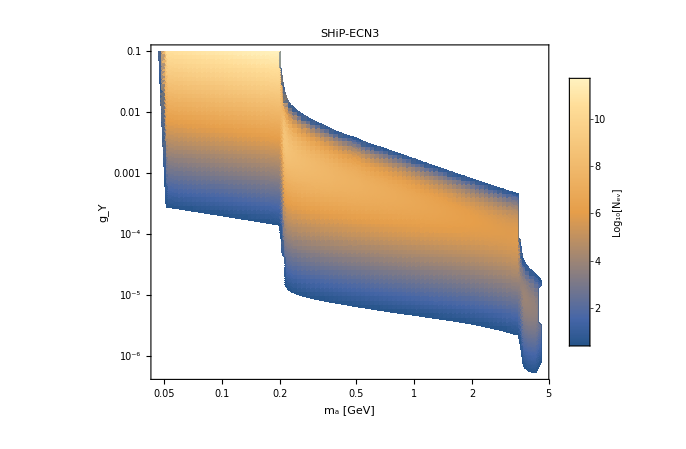

```mathematica
Nevmax=Max[Table[Max[NeventsTabulatedList[[i]][[All,3]]],{i,1,Length[NeventsTabulatedList],1}]];
plot=DensityPlot[Evaluate[Log10[NevTot[mV,ϵ2]]],{mV,maminmaxOverall[[1]],maminmaxOverall[[2]]},{ϵ2,gYminmaxoverall[[1]],gYminmaxoverall[[2]]},ScalingFunctions->{"Log","Log"},PlotPoints->100,AspectRatio->0.78,PlotRange->{All,All,{Log10[2.3],Log10[Nevmax]}},ImageSize->Large,FrameLabel->{"m_a [GeV]","g_Y"}, Frame-> True, FrameStyle->Directive[Black, 25],PlotLegends->Placed[BarLegend[{Automatic,{Log10[2.3],Log10[Nevmax]}},LegendMarkerSize->340,LegendLabel->Placed["Log_10[N_ev]",Bottom],LabelStyle->{FontSize->22},Method->{FrameStyle->Black,AxesStyle->None,TicksStyle->Black}],Right],PlotLabel->Style[Row[{ExperimentFolder}],20,Black](*,FrameTicks->{{Automatic,Automatic},{TicksPlotx,None}}*)]
(*Export[FileNameJoin[{NotebookDirectory[],"NeventsDensityPlotExample.pdf"}],plot]*)
```

## Computing sensitivities

6.×10^20

The minimal number of events N_(events, min) for which the sensitivity will be computed:

2.3

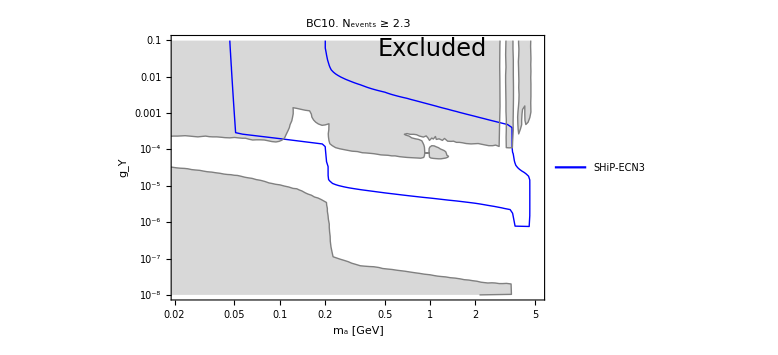

```mathematica
SensitivityBlock[Nev_,Npot_]:=Block[{},
RegSens=RegionPlot[Npot/NpotDefault NevTot[10^ma,10^gY]≥Nev,{ma,Log10[maminmaxOverall[[1]]],Log10[maminmaxOverall[[2]]]},{gY,Log10[gYminmaxoverall[[1]]],Log10[gYminmaxoverall[[2]]]}];
(*Sens={10^#[[1]],10^#[[2]]}&/@Partition[Flatten[Cases[Normal@RegSens,Line[x_]:>x,Infinity]],2];*)
SensTemp=Cases[Normal@RegSens,Line[x_]:>x,Infinity];
Sens=Table[{10^#[[1]],10^#[[2]]}&/@SensTemp[[i]],{i,1,Length[SensTemp],1}];
Export[FileNameJoin[{NotebookDirectory[],"Sensitivity domains","ALPs with fermion coupling",ExperimentFolder,ToString@StringForm["Sensitivity_ALP-fermion_at_``_Nev=``_Npot=``.xls",Sequence@@{ExperimentFolder,Nev//ToString,Npot//CForm//ToString}]}],Sens];
Sens
]
choiceNPoT=dropdownDialog[{"Yes","No"},Row[{"The number of proton collisions is ", NpotDefault,". Would you like to change it?"}]];
If[choiceNPoT=="Yes",NpotGivenExperiment=DialogInput[{br=""},Column[{"Enter the number of proton collisions",InputField[Dynamic[br],String],Button["Proceed",DialogReturn[br],ImageSize->Automatic]}]]//ToExpression//N,NpotGivenExperiment=NpotDefault]
BC10excluded=Import[FileNameJoin[{NotebookDirectory[],"contours/BC10/BC10-excluded.txt"}],"Table"];
Print["The minimal number of events N_(events, min) for which the sensitivity will be computed:"]
NevMinVal=DialogInput[{nev=""},Column[{"Enter the value of N_(events, min) for which the sensitivity will be computed:",InputField[Dynamic[nev],Number],Button["Proceed",DialogReturn[nev],ImageSize->Automatic]}]]//N
sens=SensitivityBlock[NevMinVal,NpotGivenExperiment];
Show[ListLogLogPlot[Cases[{sens,BC10excluded},_?MatrixQ,All],Joined->{True,True,True,True}, Frame-> True,FrameLabel->{"m_a [GeV]" , "g_Y"},FrameStyle->Directive[Black, 23],PlotStyle->Flatten[{ConstantArray[{Thick,Blue},If[MatrixQ[sens],1,Length@sens]],ConstantArray[{Thick,Gray},1]},1],Filling->{Length[sens]+1->{Top,Directive[Gray,Opacity[0.3]]}},ImageSize->Large,PlotRange->{{1.01maminmaxOverall[[1]],1.1maminmaxOverall[[2]]},{gYminmaxoverall[[1]],0.99gYminmaxoverall[[2]]}},PlotLabel->Style[Row[{"BC10. N_events ≥ ",NevMinVal}],18,Black],PlotLegends->Placed[Style[#,15]&/@{GivenExperimentForSensitivityComputation},{0.2,0.15}]](*,LogLogPlot[{x,x^2,x^3,x^4,x^5,x^6},{x,0.05,62.49},PlotStyle->{{Thickness[0.006],Blue},{Thickness[0.006],Darker@Red},{Thickness[0.006],Darker@Red,Dashing[0.02]},{Thickness[0.006],Black},{Thickness[0.01],Darker@Cyan,Dashing[0.007]},{Thick,Darker@Darker@Green,Dashing[0.02]},{Thick,Darker@Red}},PlotLegends->Placed[Style[#,15]&/@{"SHiP","SHADOWS_(specified in LoI)","SHADOWS_(specified by Gaia)", "SHADOWS_(collab estimate)"},{0.26,0.15}]]*),Graphics[{Text[Style["Excluded",24,Black],Scaled[{0.7,0.95}]]}]]
```